```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/Critical-region/critical_region/cheby/LPA/v1/gridnum81/buffer

```mathematica
list0=Flatten[Import["a.dat"]];
list=Flatten[Import["b.dat"]];
```

```mathematica
list1=Rest[list0];
list2=Rest[list];
```

```mathematica
ρmin=0;
ρmax=9000;
c0=1.85*10^6;
fpi=93.5;
cmax=10.^7;
cmin=10.^-2;
```

```mathematica
rhoend=10;
eqn6=Table[Evaluate[(test=SetPrecision[Sum[list1[[n]]*Cos[n*ArcCos[(2ρ-ρmin-ρmax)/(ρmax-ρmin)]],{n,1,80}]+1/2 First[list1],52])],{ρ,0,rhoend,rhoend/591}];
sigma=Table[√(2 rho),{rho,0,rhoend,rhoend/591}];
```

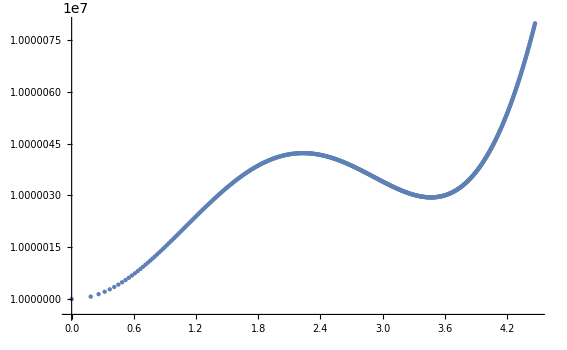

```mathematica
ListPlot[Transpose[{sigma,eqn6-eqn6[[1]]+10^7}],PlotRange->{All,All},ScalingFunctions->{Automatic,Automatic}]
```